# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Subscript[mc, dir]="../../../../mode_coupling_KPZ/calculations/";
```

```mathematica
<<(Subscript[mc, dir]<>"NFH_base.m");
```

```mathematica
(* re-definition adapted to V *)
(* dynamic programming *)
CalculateAverage[f_,{V_,p_,β_},sym_]:=CalculateAverage[f,{V,p,β},sym]=
	If[sym,(* symbolic version *)
		 Integrate[f[x]Exp[-β(V[x]+p x)],{x,(*-∞*)0,∞},Assumptions:>{p>0,β>0}]/Integrate[Exp[-β(V[x]+p x)],{x,(*-∞*)0,∞},Assumptions:>{p>0,β>0}],
		NIntegrate[f[x]Exp[-β(V[x]+p x)],{x,(*-∞*)0,∞}]/NIntegrate[Exp[-β(V[x]+p x)],{x,(*-∞*)0,∞}]]
```

## Theoretical framework

```mathematica
(* hard-core potential *)
Subscript[V, val][x_]:=If[x<0,∞,0]
```

```mathematica
(* pressure *)
Subscript[p, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=1/2;
```

```mathematica
(* alternating masses *)
Subscript[m, val]={1,3};
```

```mathematica
(* average mass *)
Subscript[m, mean]=Mean[Subscript[m, val]]
```

2

```mathematica
(* reference case for m==1 *)
csq1[{Subscript[V, val],p,β},True]
```

3 p^2 β

```mathematica
(* speed of sound, symbolic version, taking alternating masses into account *)
Subscript[c, sound,sym]=FullSimplify[Sqrt[csq[{Subscript[V, val],p,β,m},True]],Assumptions:>{p>0,β>0,m>0}]
```

√3 p √(β/m)

```mathematica
(* actual speed of sound *)
Subscript[c, sound]=csq[{Subscript[V, val],Subscript[p, val],Subscript[β, val],Subscript[m, mean]},True]^(1/2)
N[%]
```

√3

1.73205

```mathematica
(* symbolic formula for mean length (or elongation) *)
ell[{Subscript[V, val],p,β},True]
(* concrete value *)
Subscript[length, val]=%/.{p->Subscript[p, val],β->Subscript[β, val]}
```

1/(p β)

1

```mathematica
(* symbolic formula for mean energy *)
En[{Subscript[V, val],p,β},True]
(* concrete value *)
Subscript[en, val]=%/.{β->Subscript[β, val]}
```

1/(2 β)

1

```mathematica
(* "rotation" matrix R, see Eq. (B.8) *)
1/(√6){{-β p,-√(3β/m),2β},{2β p,0,2β},{-β p,√(3β/m),2β}};
(* check *)
Norm[FullSimplify[%-R[{Subscript[V, val],p,β,m},True],Assumptions:>{p>0,β>0,m>0}]]
```

0

```mathematica
Subscript[R, val]=R[{Subscript[V, val],Subscript[p, val],Subscript[β, val],Subscript[m, mean]},True];
%//MatrixForm
```

(-1/(√6) | -1/(2 √2) | 1/(√6)
√(2/3) | 0 | 1/(√6)
-1/(√6) | 1/(2 √2) | 1/(√6))

```mathematica
(* inverse "rotation" matrix R^-1 *)
Subscript[Rinv, val]=Rinv[{Subscript[V, val],Subscript[p, val],Subscript[β, val],Subscript[m, mean]},True];
%//MatrixForm
```

(-1/(√6) | √(2/3) | -1/(√6)
-√2 | 0 | √2
√(2/3) | √(2/3) | √(2/3))

```mathematica
(* check *)
Norm[Subscript[Rinv, val].Subscript[R, val]-IdentityMatrix[3]]
```

0

```mathematica
(* pointwise squares *)
Subscript[Rinv, val]^2//MatrixForm
```

(1/6 | 2/3 | 1/6
2 | 0 | 2
2/3 | 2/3 | 2/3)

```mathematica
(* G matrices only depend on sound speed *)
```

```mathematica
Subscript[G, 1,sym]=Subscript[c, sound,sym]/(2 √6){{-2,-1,2},{-1,0,-1},{2,-1,2}};
```

```mathematica
Subscript[G, 0,sym]=Subscript[c, sound,sym]/(√6){{-1,0,0},{0,0,0},{0,0,1}};
```

```mathematica
Subscript[G, -1,sym]=-Subscript[c, sound,sym]/(2 √6){{2,-1,2},{-1,0,-1},{2,-1,-2}};
```

```mathematica
(* check *)
Table[Norm[FullSimplify[Table[G[σ,i,j,{Subscript[V, val],p,β,m},True],{i,-1,1},{j,-1,1}]-Subscript[G, σ,sym],Assumptions:>{p>0,β>0,m>0}]],{σ,-1,1}]
```

{0,0,0}

```mathematica
(* check: Subscript[G, -1] == -AntiTranspose[Subscript[G, 1]] *)
Norm[Subscript[G, -1,sym]+Table[Subscript[G, 1,sym]⟦2-j,2-i⟧,{i,-1,1},{j,-1,1}]]
```

0

```mathematica
(* actual values *)
Table[Subscript[G, σ]=Subscript[G, σ,sym]/.{p->Subscript[p, val],β->Subscript[β, val],m->Subscript[m, mean]},{σ,-1,1}];
```

```mathematica
(* example *)
Subscript[G, 1]//MatrixForm
```

(-1/(√2) | -1/(2 √2) | 1/(√2)
-1/(2 √2) | 0 | -1/(2 √2)
1/(√2) | -1/(2 √2) | 1/(√2))

```mathematica
(* Eq. (4.7) in "Nonlinear fluctuating hydrodynamics for anharmonic chains" *)
Subscript[λ, s]=2 √2 Abs[Subscript[G, 1]⟦3,3⟧]
```

2

## Evaluate equilibration

```mathematica
(* exact "average" by construction (up to numerical precision) *)
Subscript[avr, 0]=Import["microcanonical_test_avr0.dat","Real64"]
Subscript[avr, 1]=Import["microcanonical_test_avr1.dat","Real64"]
```

{1.,9.35912×10^-17,1.}

{1.,9.35912×10^-17,1.}

```mathematica
Subscript[sqrs, val]=Partition[Partition[Import["microcanonical_test_sqrs.dat","Real64"],3],3];
Dimensions[%]
```

{16,3,3}

```mathematica
(* calculate covariance matrix *)
Subscript[S, mat]=#-KroneckerProduct[Subscript[avr, 0],Subscript[avr, 1]]&/@Subscript[sqrs, val];
Dimensions[%]
```

{16,3,3}

```mathematica
(* sum should be zero due to conservation laws *)
Norm[Total[Subscript[S, mat]]]
```

2.23484×10^-13

```mathematica
(* example: Subscript[r, j] correlation *)
Subscript[S, mat]⟦1;;5,1,1⟧
```

{0.883196,-0.0588382,-0.0590293,-0.0589466,-0.0586243}

```mathematica
(* example: Subscript[p, j] correlations *)
Subscript[S, mat]⟦;;,2,2⟧
```

{3.93459,-0.200729,-0.331358,-0.198304,-0.331816,-0.19962,-0.332452,-0.202677,-0.340681,-0.202677,-0.332452,-0.19962,-0.331816,-0.198304,-0.331358,-0.200729}

```mathematica
(* example: Subscript[e, j] correlations *)
Subscript[S, mat]⟦;;,3,3⟧
```

{1.65213,-0.113327,-0.107448,-0.112133,-0.107721,-0.113532,-0.106076,-0.114176,-0.103299,-0.114176,-0.106076,-0.113532,-0.107721,-0.112133,-0.107448,-0.113327}

```mathematica
(* example: Subscript[r, j]-Subscript[p, j] correlations *)
Subscript[S, mat]⟦;;,1,2⟧
```

{0.00413076,-0.00262101,-0.000420262,-0.000511434,0.00233816,-0.000939269,-0.00177113,0.00120626,0.00185921,0.00223897,-0.000461161,-0.00076194,-0.00200352,-0.00236779,0.000191531,-0.000107359}

## Visualize results

```mathematica
Subscript[plt, label]="hard-points with m_0="<>ToString[Subscript[m, val]⟦1⟧]<>", m_1="<>ToString[Subscript[m, val]⟦2⟧]<>", N="<>ToString[Length[Subscript[S, mat]]]<>",\nell="<>ToString[Subscript[length, val]]<>", e="<>ToString[Subscript[en, val]]<>", c="<>ToString[InputForm[Subscript[c, sound]]]<>", runs=10^5";
```

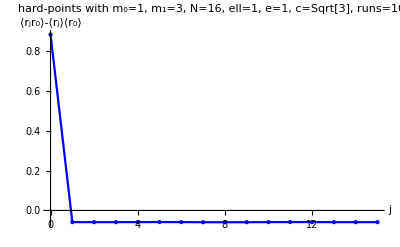

```mathematica
ListLinePlot[Transpose[{Range[0,Length[Subscript[S, mat]]-1],Subscript[S, mat]⟦;;,1,1⟧}],PlotLabel->Subscript[plt, label],PlotRange->All,Mesh->All,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"j","⟨r_jr_0⟩-⟨r_j⟩⟨r_0⟩"}]
Export[FileBaseName[NotebookFileName[]]<>"_r_corr.pdf",%];
```

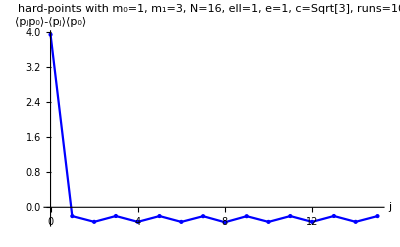

```mathematica
ListLinePlot[Transpose[{Range[0,Length[Subscript[S, mat]]-1],Subscript[S, mat]⟦;;,2,2⟧}],PlotLabel->Subscript[plt, label],PlotRange->All,Mesh->All,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"j","⟨p_jp_0⟩-⟨p_j⟩⟨p_0⟩"}]
Export[FileBaseName[NotebookFileName[]]<>"_p_corr.pdf",%];
```

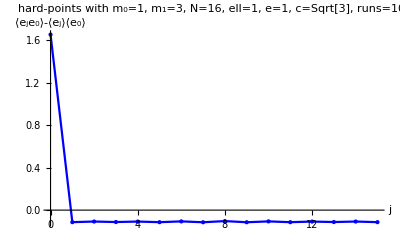

```mathematica
ListLinePlot[Transpose[{Range[0,Length[Subscript[S, mat]]-1],Subscript[S, mat]⟦;;,3,3⟧}],PlotLabel->Subscript[plt, label],PlotRange->All,Mesh->All,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"j","⟨e_je_0⟩-⟨e_j⟩⟨e_0⟩"}]
Export[FileBaseName[NotebookFileName[]]<>"_e_corr.pdf",%];
```